```mathematica
<<VilCretas`
```

VilCretas está disponible.

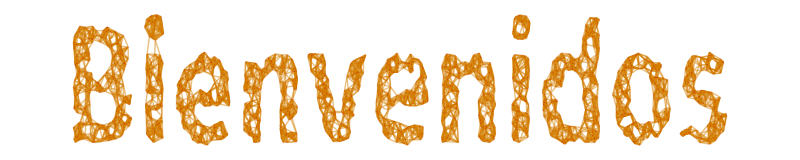

```mathematica
GrafoString["Bienvenidos"]
```

```mathematica
-Graphics--Graphics-
```

```mathematica
A={93,90,5,54,55,25};
R={{93,25},{90,5},{5,55},{5,25},{5,54},{5,5},{55,55},{55,25},{25,5},{54,54},{54,25},{25,90},{54,5},{54,93},{54,90}};
```

```mathematica
MatrizRelBin[R,A,A, encabezados->True]
```

| 93 | 90 | 5 | 54 | 55 | 25
93 | 0 | 0 | 0 | 0 | 0 | 1
90 | 0 | 0 | 1 | 0 | 0 | 0
5 | 0 | 0 | 1 | 1 | 1 | 1
54 | 1 | 1 | 1 | 1 | 0 | 1
55 | 0 | 0 | 0 | 0 | 1 | 1
25 | 0 | 1 | 1 | 0 | 0 | 0

# tutorias@una.cr 2562-6771 mariana.ramirez.sandi@una.cr 7016-8340

```mathematica
R1={{99,55},{85,13},{99,74},{85,100},{22,100},{100,45},{85,74},{99,99},{100,100},{100,80}};
R2={{99,55},{13,85},{99,74},{85,100},{22,100},{100,45},{85,74},{99,99},{100,100},{100,80}};
R3={{99,55},{85,13},{99,74},{85,100},{22,100},{45,100},{85,74},{99,99},{100,100},{100,80}};
R4={{99,55},{13,13},{99,74},{85,100},{22,100},{100,45},{85,74},{99,99},{100,100},{100,80}};
R5={{99,55},{85,13},{99,74},{85,100},{22,100},{100,45},{85,74},{99,99},{100,100},{80,80}};
```

```mathematica
R = {{99,55},{85,13},{99,74},{85,100},{22,100},{100,45},{85,74},{99,99},{100,100},{100,80}};
```

```mathematica
Table[ElementRelBinQ[R,i],{i,R1}]
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[ElementRelBinQ[R,i],{i,R2}]
```

{True,False,True,True,True,True,True,True,True,True}

```mathematica
Table[ElementRelBinQ[R,i],{i,R3}]
```

{True,True,True,True,True,False,True,True,True,True}

```mathematica
Table[ElementRelBinQ[R,i],{i,R4}]
```

{True,False,True,True,True,True,True,True,True,True}

```mathematica
Table[ElementRelBinQ[R,i],{i,R5}]
```

{True,True,True,True,True,True,True,True,True,False}

```mathematica
<<TutoriasED`
```

```mathematica
existeElementoRelBin[R,R1]
```

Tabla de Elementos y su Relación Binaria:

Elemento | Relación Binaria
{99,55} | True
{85,13} | True
{99,74} | True
{85,100} | True
{22,100} | True
{100,45} | True
{85,74} | True
{99,99} | True
{100,100} | True
{100,80} | True

```mathematica
A=Range[-5,1000,3];
```

```mathematica
B=Range[5,998,3];
```

```mathematica
Length[PC[A,B]]
```

111552

```mathematica
PC[A,B]//Length
```

111552

```mathematica
A=Range[20];
```

```mathematica
R=RelBin["Mod[a^2+b^2,2]!=0&&a^3-b^3<=41",A,A];
```

```mathematica
Length[DominioRelBin[R]]
```

19

```mathematica
R//Length
```

103

```mathematica
Mod[a^2+b^2,2]!=0
OddQ[a^2+b^2]==True
EvenQ[a^2+b^2]!=True
```

```mathematica
RelacionComposicion[R1_,R2_]:=Module[{Composicion={},i,j},For[i=1,i≤Length[R2],For[j=1,j≤Length[R1],If[R2[[i,2]]==R1[[j,1]],Composicion=Append[Composicion,{R2[[i,1]],R1[[j,2]]}]];j++];
i++];DeleteDuplicates[Composicion]]
```

```mathematica
R1={{0,0},{5,5},{5,12},{12,0},{16,16}};
R2={{0,18},{0,24},{5,17},{12,19},{16,23}};
```

```mathematica
R=RelacionComposicion[R2,R1]
```

{{0,18},{0,24},{5,17},{5,19},{12,18},{12,24},{16,23}}

```mathematica
respuestas={{10,24},{0,24},{7,21},{0,18},{5,17}};
```

```mathematica
existeElementoRelBin[R, respuestas]
```

Tabla de Elementos y su Relación Binaria:

Elemento | Relación Binaria
{10,24} | False
{0,24} | True
{7,21} | False
{0,18} | True
{5,17} | True

```mathematica
ElementRelBinQ[R,{5,17}]
```

True

```mathematica
A={44,62,24,98,85,43,68,35,69,77};
R=RelBin["Mod[a^2-b^2,5]==0",A,A]
```

{{44,44},{44,24},{44,69},{62,62},{62,98},{62,43},{62,68},{62,77},{24,44},{24,24},{24,69},{98,62},{98,98},{98,43},{98,68},{98,77},{85,85},{85,35},{43,62},{43,98},{43,43},{43,68},{43,77},{68,62},{68,98},{68,43},{68,68},{68,77},{35,85},{35,35},{69,44},{69,24},{69,69},{77,62},{77,98},{77,43},{77,68},{77,77}}

```mathematica
ClasesEquivalencia[R,A]
```

[44]={44,24,69}

[62]={62,98,43,68,77}

[24]={44,24,69}

[98]={62,98,43,68,77}

[85]={85,35}

[43]={62,98,43,68,77}

[68]={62,98,43,68,77}

[35]={85,35}

[69]={44,24,69}

[77]={62,98,43,68,77}

El conjunto de clases de equivalencia distintas es:

{{44,24,69},{62,98,43,68,77},{85,35}}

```mathematica
A={29,18,1,65,68,69,12,17,59,23,32,21,49,38,2};
```

```mathematica
R=RelBin["Mod[a^2-1,b^2-1]==0",A,A];
```

```mathematica
ClasificacionRelBin[R,A]
```

{False,False,True,True}

```mathematica
TipoRelacion[R,A]
```

La relación no es reflexiva, un contraejemplo es: {1,1} no pertenece

La relación no es simétrica, un contraejemplo es: {29,2} está en la relación pero {2,29} no pertenece

La relación es antisimétrica

La relación es transitiva

```mathematica
?ClasificacionRelBin
```

```mathematica
ClasesEquivalencia[R,A]
```